## 前沿

## 质数分布

```mathematica
Plot[{PrimePi[x],x/Log[x],LogIntegral[x],RiemannR[x]},{x,1.5,100},PlotLabels->"Expressions",PlotTheme->"Detailed",PlotLegends->None]
```

-Graphics-

## 吉布斯现象

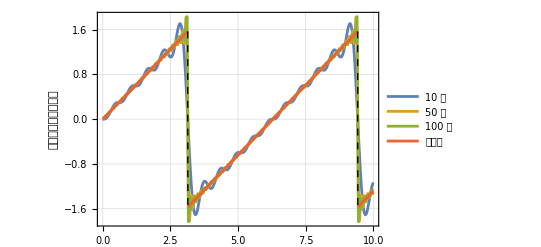

```mathematica
Sum[(-1)^(i-1)Sin[i x]/i,{i,1,#}]&/@{10,50,100,Infinity}//Plot[#,{x,0,10},ExclusionsStyle->Dashed,PlotTheme->"Detailed",PlotLegends->{"10 项","50 项","100 项","锯齿波"},FrameLabel->{"","傅里叶级数前项求和"}]&
```

## 莫比乌斯环

```mathematica
ParametricPlot3D[{Cos[t] (3+r Cos[t/2]),Sin[t] (3+r Cos[t/2]),r Sin[t/2]},{r,-1,1},{t,0,2 Pi}]
```

-Graphics3D-

图形上的参考线好像就是“测地线”